# Practical 4 Regula Falsi Method

```mathematica
(1)   Find out the root of the function g(x)=x^3-5x+1 after  10 iterations of the Regula Falsi method.
```

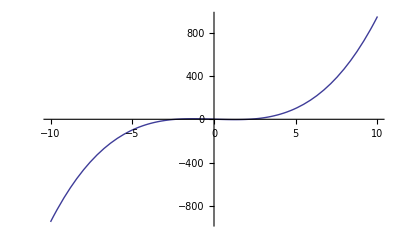

i | interval | xi | f[xi]
1 | [-1.,1.] | 0.25 | -0.234375
2 | [-1.,0.25] | 0.19402985 | 0.037155501
3 | [0.194029850746,0.25] | 0.20168865 | -0.00023892045
4 | [0.194029850746,0.201688654959] | 0.20163972 | -2.2244344×10^-7
5 | [0.194029850746,0.201639721325] | 0.20163968 | -2.0708324×10^-10
6 | [0.194029850746,0.201639675766] | 0.20163968 | -1.9273472×10^-13
7 | [0.194029850746,0.201639675723] | 0.20163968 | -4.4408921×10^-16
8 | [0.194029850746,0.201639675723] | 0.20163968 | 1.110223×10^-16
9 | [0.201639675723,0.201639675723] | 0.20163968 | 1.110223×10^-16
10 | [0.201639675723,0.201639675723] | 0.20163968 | -2.220446×10^-16

Root after 10 iterations 0.20163968

Function value at approximated root,f[xi]= -2.220446×10^-16

```mathematica
RegulaFalsi[x0_,x1_,n_,f_]:=Module[{xk,xk1,xk2},xk=N[x0];xk1=N[x1];If[f[xk]*f[xk1]>0,Print["We cannot continue with Regula Falsi method as function values are not opposite sign at end points of interval"];Return[]];i=1;Output={ };
While[i≤n,xk2=(xk*f[xk1]-xk1*f[xk])/(f[xk1]-f[xk]);interval="["<>ToString[NumberForm[xk,12]]<>","<>ToString[NumberForm[xk1,12]]<>"]"; 
Output=Append[Output,{i,interval,xk2,f[xk2]}];If[Sign[f[xk1]]==Sign[f[xk2]],xk1=xk2,xk=xk2];i++;];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"i","interval","xi","f[xi]"}}],8]];
Print[" Root after ",n," iterations ",NumberForm[xk2,8]];
Print[" Function value at approximated root,f[xi]= ",NumberForm[f[xk2],8]];];
g[x_]:=x^3-5x+1;
Plot[g[x],{x,-10,10}]
RegulaFalsi[-1,1,10,g]
```

```mathematica
(2)  Find out the  root of the function f(x)=x^4-3 x^2+x-10 over the interval  [2,3] after  7 iterations of the Regula Falsi method.
```

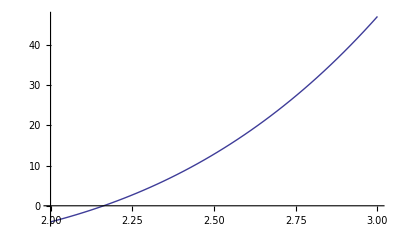

i | interval | xi | f[xi]
1 | [2.,3.] | 2.0784314 | -2.2198625
2 | [2.07843137255,3.] | 2.119995 | -1.1637008
3 | [2.11999499205,3.] | 2.1412571 | -0.59162874
4 | [2.14125711528,3.] | 2.1519325 | -0.29607559
5 | [2.15193245843,3.] | 2.1572414 | -0.1469951
6 | [2.15724139986,3.] | 2.159869 | -0.072691406
7 | [2.15986895617,3.] | 2.1611663 | -0.035876602

Root after 7 iterations 2.1611663

Function value at approximated root,f[xi]= -0.035876602

```mathematica
f[x_]:=x^4-3 x^2+x-10;
Plot[f[x],{x,2,3}]
RegulaFalsi[2,3,7,f]
```